```mathematica
ClearAll["Global`*"] 

(* non-molecule means single instanton *)
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=20
(*Number of Time Steps:*)
n:=20
(*Integration Bounds*)
l:=5
(*Unit conversion from ρ^-1 to GeV and instanton density 7
E:what density used?
*)
units1:=2*25.5
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},
{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Test Values*)
ypoint={1.,1.,0.,0.};
```

```mathematica
(*Regular gauge*)
(*A[y_]:=Table[Sum[2η[[μ,ν,aa]]*y[[ν]]/(y.y+1),{ν,1,4}],{μ,1,4},{aa,1,3}]
Dimensions[A[ypoint]]*)
(*Singular gauge*)
A[y_]:=Table[Sum[2ηbar[[μ,ν,aa]]*y[[ν]]/((y.y+1)(y.y)),{ν,1,4}],{μ,1,4},{aa,1,3}]
Dimensions[A[ypoint]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
```

```mathematica
(*Table of wilson lines along L*)
WList1[y_]:=Table[W2[A[y+{0,0,0,(i-1/2)L/n}]],{i,1,n}]
WdList1[y_]:=Table[Wd2[A[y+{0,0,0,(i-1/2)L/n}]],{i,1,n}]
```

```mathematica
ImesDipole1[y_,r_]:=Module[{WD=IdentityMatrix[2]},
For[i=1,i<=n,i++,
WD=Normal[Series[WList1[y+{rr/2,0,0,0}][[i]].WD.WdList1[y-{rr/2,0,0,0}][[i]],{rr,0,3}]];
];
1-1/2*Tr[WD/.rr->r]
]
ImesDipole1[ypoint,0.5]
```

0.00116127+0. ⅈ

```mathematica
(*Matrix Product*)
Wapprox1[y_]:=Dot@@WList1[y] (* applies the function to everything in the table *)
Wdapprox1[y_]:=Dot@@WdList1[y]
```

```mathematica
Imes1[y_,rr_]:=1-1/2Tr[Wapprox1[y+{rr/2,0,0,0}].Wdapprox1[y-{rr/2,0,0,0}]](* integrand *)
```

```mathematica
AbsoluteTiming[Imes1[ypoint,0.5]]
AbsoluteTiming[ImesDipole1[ypoint,0.5]]
```

{0.0186536,0.001161+0. ⅈ}

{0.255469,0.00116127+0. ⅈ}

```mathematica
(*1s timing, which is bad, but it is many orders of magnitude smaller*)
```

```mathematica
AbsoluteTiming[units1*NIntegrate[Imes1[{y1,y2,y3,0},0.25],{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]]
```

$Aborted

```mathematica
IntDataMes=Table[{rr,units1*NIntegrate[Imes1[{y1,y2,y3,0},rr],{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{rr,0,40,4}]
```

$Aborted

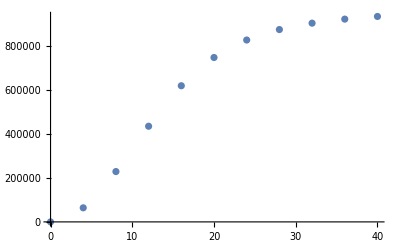

```mathematica
p1=ListPlot[IntDataMes]
```

```mathematica
RandY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*Number of test points for monte carlo*)
num=1000;
l=5;
```

```mathematica
(*Random numbers for all future points*)
randY1=Table[RandY,11,num];
```

```mathematica
AbsoluteTiming[units1*8l^3/num*Sum[Imes1[randY1[[1,i]],0.25],{i,1,num}]]
```

{53.8182,53.4295+0. ⅈ}

```mathematica
MCDataMes=Table[{rr,units1*8l^3/num*Sum[Imes1[randY1[[rr/0.4+1,i]],rr],{i,1,num}]},{rr,0,4,0.4}]
```

{{0.,2.06668×10^-12+0. ⅈ},{0.4,45.5548+0. ⅈ},{0.8,299.22+0. ⅈ},{1.2,243.866+0. ⅈ},{1.6,493.799+0. ⅈ},{2.,665.521+0. ⅈ},{2.4,636.581+0. ⅈ},{2.8,749.339+0. ⅈ},{3.2,726.938+0. ⅈ},{3.6,967.916+0. ⅈ},{4.,841.547+0. ⅈ}}

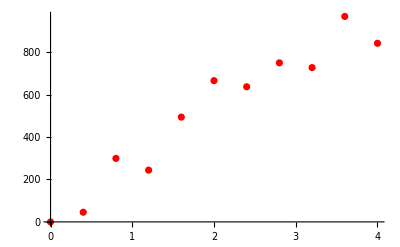

```mathematica
p2=ListPlot[MCDataMes, PlotStyle->Red]
```

```mathematica
(*Using the analytic definitions from WilsonLineDefinitions*)
Imes1A[y_, ct_,r_]:=N[(1-1/2*Tr[W2[A1[y^2,1],Nv[0,y,ct]].Wd2[A1[y^2+r^2-2r*y*ct,1],Nv[r,y,ct]]])]
```

```mathematica
ADataMes=Table[{r,units1*NIntegrate[Imes1A[Sqrt[y1^2+y2^2+y3^2],y1/Sqrt[y1^2+y2^2+y3^2], r],{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]},{r,0,4,0.4}]
```

{{0.,-2.15174×10^-12+0. ⅈ},{0.4,64.7055},{0.8,221.017},{1.2,400.169},{1.6,558.552},{2.,684.048},{2.4,778.949},{2.8,848.805},{3.2,897.809},{3.6,927.638},{4.,936.268}}

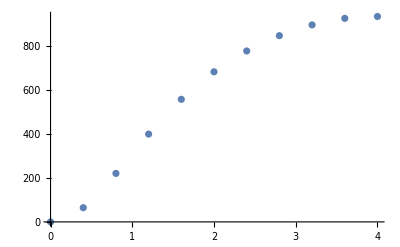

```mathematica
pA=ListPlot[ADataMes]
```

```mathematica
(* comparison of analytic and numerical--singular gauge works very well!*)
```

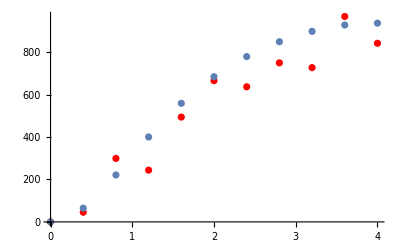

```mathematica
Show[p2,pA]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[A[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[A[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]A[{y[1],y[2],y[3],y[4]}][[mu]][[b]]A[{y[1],y[2],y[3],y[4]}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
```

```mathematica
FF[yy_]:=1/4*Sum[Fmunu[[mu,nu,a]]Fmunu[[mu,nu,a]],{mu,1,4},{nu,1,4},{a,1,3}]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]}
```

```mathematica
FF[ypoint]
```

0.592593

```mathematica
NIntegrate[FF[{y1,y2,y3,y4}],{y1,-l,l},{y2,-l,l},{y3,-l,l},{y4,-l,l}]/(8Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 78.9549 and 0.000411567 for the integral and error estimates.

```mathematica
0.9999758854529343

(* comparison action calculation, numerics to analytitc, OK *)
```

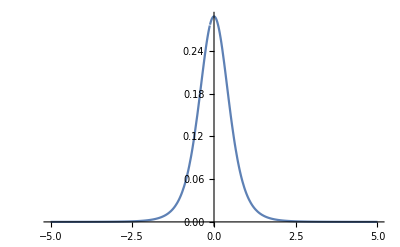

```mathematica
(*Comparison of analytical and numeric time integral*)
p1a=Plot[Imes1A[y+0.125,1,0.25],{y,-5,5},PlotRange->All]
```

```mathematica
L=20;
n=20;
```

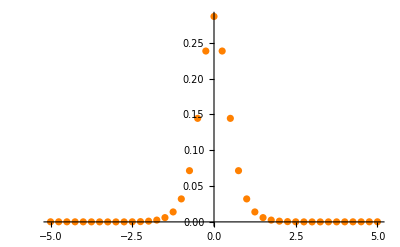

```mathematica
p1n=ListPlot[Table[{y,ImesDipole1[{y,0,0,0},0.25]},{y,-5.,5.,0.25}],PlotStyle->Orange,PlotRange->All]
```

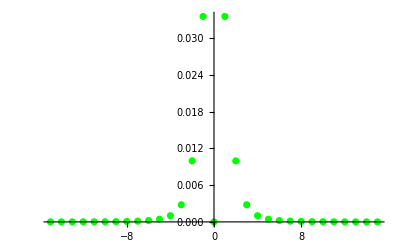

```mathematica
p1n2=ListPlot[Table[{y,y^2(Imes1[{y,0,0,0},0.25])},{y,-15.,15.,1}],PlotStyle->Green,PlotRange->All]
```

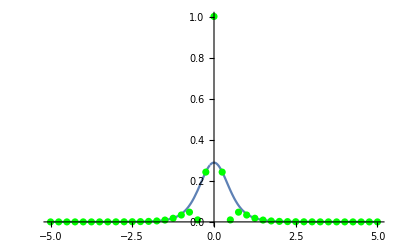

```mathematica
(*The analytic solution does not go to 0 at y=6*)
Show[p1a,p1n2]
```

```mathematica
AbsoluteTiming[Imes1[{4.,0,0,0},0.25]]
AbsoluteTiming[ImesDipole1[{4.,0,0,0},0.25]]
AbsoluteTiming[Imes1A[4+0.125,1,0.25]]
```

{0.0394265,0.0000818154+0. ⅈ}

{0.996908,0.0000820644+0. ⅈ}

{0.0001005,0.000062991+0. ⅈ}

```mathematica
l=5;
```

```mathematica
units1*8l^3/num*Sum[Imes1[randY1[[1,i]],0.25],{i,1,num}]
```

$Aborted

```mathematica
units1*8l^3/num*Sum[ImesDipole1[randY1[[1,i]],0.25],{i,1,num}]
```

225.423+0. ⅈ

```mathematica
units1*NIntegrate[Imes1A[Sqrt[y1^2+y2^2+y3^2],y1/Sqrt[y1^2+y2^2+y3^2], 0.5],{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2]
```

97.9121